```mathematica
MmaData=Table[
m=Floor[500 1.2^p];
A=RandomReal[{-1,1},{m,m}];
t=Timing[QRDecomposition[A];]⟦1⟧;
{m,t},
{p,1,11}]
```

{{600,0.03125},{720,0.015625},{864,0.015625},{1036,0.046875},{1244,0.0625},{1492,0.140625},{1791,0.234375},{2149,0.375},{2579,0.5625},{3095,1.01563},{3715,1.57813}}

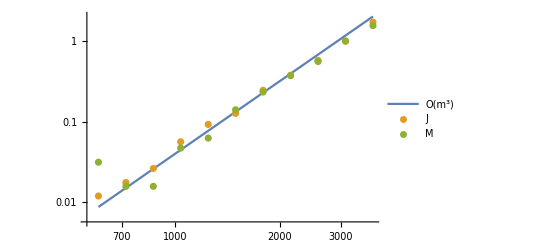

```mathematica
JuliaData=Import["C:\\Users\\AllanStruthers\\Desktop\\TimingData.csv"];
CubicData=Table[m=500 1.2^p;{m,0.4 10^-10 m^3},{p,1,11}];
ListLogLogPlot[{CubicData,JuliaData, MmaData},PlotLegends->{"O(m^3)","J","M"},
Joined->{True,False,False}]
```